```mathematica
(*This work is licensed under the Creative Commons 4.0 License.
To view a copy of the license,visit http://creativecommons.org/licenses/by/4.0/
-Graphics-
Benjamin Schäfer, Max Planck Institute for Dynamics and Self-Organizaion, 2018
benjamin.schaefer@ds.mpg.de
*)
```

```mathematica
(*Import PowerGridPackage*)
SetDirectory[NotebookDirectory[]];
Get["PowerGridCompact.m"]
```

# (*Elementary examples for Power grid cascade simulations*)

How to use : Select a cell and hit “Shift+Enter”, confirm “evaluation of initialization cells” to import the PowerGridCompact package
Other networks and power distributions can be easily simulated by changing the variables “matrix” and “power”. For a systematic analysis, all potential “triggerLine” values and multiple values for “toleranceα” need to be considered.

```mathematica
(*Simulation using the sample 5 node system (from in Fig. 1)*)
```

```mathematica
(*Set the matrix and power distribution in the network*)
Clear[actualCutEdges,loadPlotT,flowsExistingLinesOverTime]
matrix=AdjacencyMatrix@EdgeAdd[EdgeAdd[CycleGraph[5],UndirectedEdge[1,3]],UndirectedEdge[2,4]];listOfEdges=EdgeList@AdjacencyGraph@matrix;
power={-1,3/2,-1,-1,3/2};
(*Run the simulation and also store the trajectory*)
fiveNodeCascadeResults=PowerGridCascadeSimulation[couplingMatrix->1.63matrix,powerVector->power,triggerLine->{2,4},toleranceα->0.6]
```

{number of nodes not synchronized after cascade→5,number of lines cut→6,lines cut→{{{2,4},1.},{{4,5},2.11834},{{2,3},2.3968},{{1,2},3.0498},{{1,5},3.16962},{{1,3},3.2689}},distanceMatrix→{{0,1.},{1,2.11834},{1,2.3968},{1,3.0498},{1,3.16962},{1,3.2689}},nodes not synchronized after cascade→{1,2,3,4,5},redundant (0-flow) lines→{}}

{number of nodes not synchronized after cascade→98,number of lines cut→14,lines cut→{{17<->20,1.},{{57,59},1.55527},{{57,60},1.61858},{{57,61},1.79388},{{44,58},2.31464},{{58,62},2.51782},{{30,53},2.71635},{{30,43},2.9232},{{94,95},3.56538},{{26,31},3.89059},{{30,52},4.49956},{{60,71},5.11508},{{53,73},5.336},{{93,94},6.63372}},distanceMatrix→{{0,1.},{3,1.55527},{3,1.61858},{3,1.79388},{3,2.31464},{3,2.51782},{3,2.71635},{4,2.9232},{7,3.56538},{4,3.89059},{4,4.49956},{4,5.11508},{3,5.336},{7,6.63372}},nodes not synchronized after cascade→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98},redundant (0-flow) lines→{{42,46},{82,83}}}

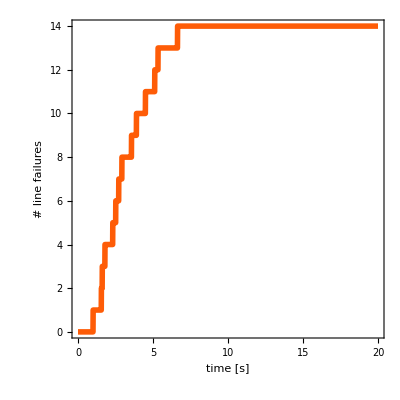

```mathematica
(*Simulation using the Spnish distributed grid (cutting line 1, as in Fig. 2): Takes several seconds to a few minutes*)
(*Import the data*)
SetDirectory[NotebookDirectory[]];SetDirectory["NetworkData"];
matrix=Import["SpanishDistributedPower_Matrix.csv"];
power=Flatten@Import["SpanishDistributedPower_Power.csv"];
listOfEdges=EdgeList[AdjacencyGraph[Map[Unitize,matrix,2]]];
(*Run the simulation*)
cascadeResult=PowerGridCascadeSimulation[powerVector->power,couplingMatrix->matrix,triggerLine->listOfEdges[[35]],toleranceα->0.52]
(*Plot the line failures over line*)
linesCut=DeleteCases["lines cut"/.cascadeResult,"lines cut"]⟦1;;All,2⟧;
linesCutOverTime=Table[{t,Length[Cases[linesCut,x_/;x<t]]},{t,0,20,0.01}];
ListLinePlot[linesCutOverTime,Frame->True,FrameLabel->{"time [s]","# line failures"},LabelStyle->Directive[20,Bold],PlotStyle->Directive[Thickness[0.01],ColorData[3,"ColorList"][[2]]],AspectRatio->1]
```

```mathematica
(*Simulation and trajectories using the sample 5 node system (as in Fig. 1)*)
```

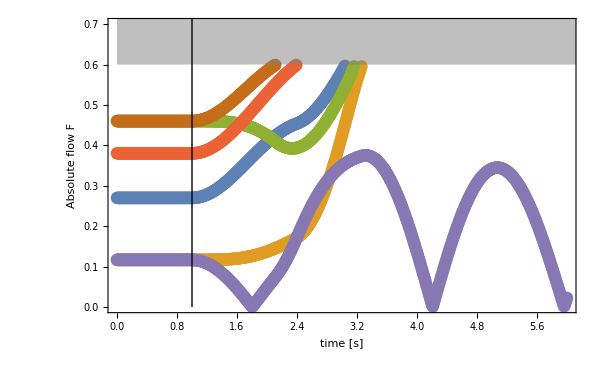

```mathematica
(*Set the matrix and power distribution in the network*)
Clear[actualCutEdges,loadPlotT,flowsExistingLinesOverTime]
matrix=AdjacencyMatrix@EdgeAdd[EdgeAdd[CycleGraph[5],UndirectedEdge[1,3]],UndirectedEdge[2,4]];listOfEdges=EdgeList@AdjacencyGraph@matrix;
power={-1,3/2,-1,-1,3/2};numberOfNodes=5;
(*Run the simulation and also store the trajectory*)
fiveNodeCascadeResults=PowerGridCascadeSimulation[couplingMatrix->1.63matrix,powerVector->power,triggerLine->{2,4},toleranceα->0.6];
fiveNodeSolution=PowerGrid`sol;
angles=Table[PowerGrid`angleθ[i],{i,1,numberOfNodes}]/.fiveNodeSolution[[1]]; linkList=EdgeList[AdjacencyGraph[matrix]];
linesCut=(DeleteCases["lines cut"/.fiveNodeCascadeResults,"lines cut"]);
actualCutEdges[t_]:=DeleteCases[Table[If[linesCut[[i,2]]<t,Apply[UndirectedEdge,linesCut[[i,1]]],Nothing],{i,1Length[linesCut]}],Nothing,Infinity];
flowsExistingLinesOverTime[tMax_,tStepSize_,angles_,linkList_]:=Table[Table[{t,If[MemberQ[actualCutEdges[t],link],10,Abs@Sin[angles[[link[[1]]]][t]-angles[[link[[2]]]][t]]]},{t,0,tMax,tStepSize}],{link,linkList}];
(*Plot the five node trajectory*)
numberOfNodes=5;thick=0.013;markerSize=.015;
plotStyle=Table[Thickness[thick],{numberOfNodes+2}];plotStyle[[Position[linkList,UndirectedEdge@@{2,4}][[1,1]]]]=Directive[Thickness[thick],Dashed];
plotLegends=Map[Subscript["F",ToString[#]]&,DeleteCases[linkList,UndirectedEdge@@{2,4}]];
loadPlotT[tmax_,tStepSize_,plotTmax_]:=
With[{},
thresholdList=Table[{t,0.6},{t,0,tmax,tStepSize}];
Show[ListPlot[flowsExistingLinesOverTime[tmax,tStepSize,angles,DeleteCases[linkList,UndirectedEdge@@{2,4}]],ImageSize->{600,400},Frame->True,FrameLabel->{"time [s]","Absolute flow F"},LabelStyle->Directive[Bold, 20],PlotStyle->PointSize[markerSize],PlotRange->{{0,plotTmax},{0,0.7}}],Plot[0.6,{t,0,10},PlotStyle->Transparent,Filling->Top,FillingStyle->Directive[Opacity[0.5],Gray]],Graphics[{Thick,Line[{{1,0},{1,100}}]}],PlotRangeClipping->True]]
cascadeFlowPlot=loadPlotT[6,0.01,6]
```